Note:
This Notebook employs a non-default Stylesheet. Input cells with code for user-defined functions (and “useful Global variables”) are specified via ⌘-shift-D rather than ⌘-9 as for standard Input cells. They are Evaluatable Initialization cells with a light grey background specified by RGBColor[{0.925,0.925,0.958}].

Note:
Full execution of this Notebook takes around 870 seconds.

(* useful Global variables *)
figNo=1;
captionStyle={FontFamily→ "Book Antiqua", FontSize→16};
$Line=0;

# Digitizing DB’s Noisy Gaussian Data Revision 4

## Packages

```mathematica
Needs[ "IP`" ]
functionListing[ "IP`"]
functionCount[ "IP`"]
```

## Functions

#### trueCoords[{x_, y_}]

ClearAll[trueCoords]
trueCoords::usage = "trueCoords[{x,y}] gives the ''true'' coordinates of the point with ''graphics'' coordinates {x,y} once the Global variables xWest, ySouth, coordsOrigin, xScaleFactor, and yScaleFactor are defined.";
trueCoords[{x_, y_}] := {(x - coordsOrigin[[1]])*xScaleFactor, (y - coordsOrigin[[2]])*yScaleFactor} + {xWest, ySouth}
trueCoords[ x_] := (x - coordsOrigin[[1]])*xScaleFactor + xWest
?trueCoords

#### curvatureFunction[ func_(InterpolatingFunction, Symbol, Function, NetChain) ]

```mathematica
Remove[ curvatureFunction ]
curvatureFunction::usage="curvatureFunction[arg] is an overloaded function.
If the input has Head NetChain (e.g., curvetrained), curvatureFunction[curvetrained,p] calculates the curvature of curvetrained[] at x. Note that even though curvature is property of a curve at a point x, a ''local'' InterpolatingFunction object has to be constructed to fit the NetChain fitting function in a small region around x so that effectively the curve represented by curvetrained can be differentiated at x.
If the input has Head Symbol (e.g., func), curvatureFunction[func] constructs the curvature function κ for the function y=func[x].
If the input has Head Function (e.g., func), curvatureFunction[(s↦func[s])] constructs the curvature function κ for the function y=func[x].
If the input has Head InterpolatingFunction, (e.g., interpF) curvatureFunction[interpF] constructs the curvature function for the function y=interpF[x].
Typical usage is: kurv=curvatureFunction[ … ], followed by Plot[ kurv[x], {x, xMin, xMax}].
Note that for a general unassigned input with Head Symbol, (e.g., f) the form of the curvature function is
κ[x] = f''[x]/((1+f'[x]^2)^(3/2)),
so that the curvature is—unsurprisingly—essentially a scaled version of the second derivative.
When f'[x] = 0 (at maxima and minima) the curvature is exactly f''[x].
"; 
curvatureFunction[ func_InterpolatingFunction ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
(s↦ (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->s}//Evaluate)
]
curvatureFunction[ func_Symbol ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
(s↦ (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->s}//Evaluate)
]
curvatureFunction[ func_Function ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
(s↦ (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->s}//Evaluate)
]
curvatureFunction[ annFittedFunction_NetChain, p_ ] := Module[ 
{interpF, x, y,κ} ,
(* construct InterpolationObject representation of annFittedFunction[x] in the neighborhood of p *)
interpF = Interpolation[Table[ {xx,annFittedFunction[xx] }, {xx,p-0.02 ,p+0.02,0.04/10} ]];
(* construct parametric form of y=interpF[x] *)
x[t_]:=t;
y[t_]:=interpF[t];
(* construct curvature function κ[x] for interpF[x] *)(s↦ (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->s}//Evaluate)[p]
]
?curvatureFunction
```

Construct a fitting function curvetrained159[]. This takes ~20 seconds.

```mathematica
noisyGaussianDataDBAsRules =
{-4.->0.004991403161076269,-3.6->-0.07037907665923704,-3.2->-0.16169901554677835,-2.8000000000000003->-0.0038900593517214865,-2.4000000000000004->-0.1948793030083943,-2.->-0.21992892791100527,-1.6->-0.031153444492377114,-1.2000000000000002->0.3581096808999016,-0.8->0.39191583862405666,-0.4->0.8288586174082231,0.->1.0714671524161137,0.4->1.0553625621338605,0.8->0.5738613486225081,1.2000000000000002->0.3112082799214675,1.6->0.11067978380061638,2.->0.1191982171250161,2.4000000000000004->0.32842391210035493,2.8000000000000003->0.27647782575297675,3.2->-0.13107902312694075,3.6->-0.5291931422381235,4.->0.11399057334462004};
```

```mathematica
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->159
];
(**)
curvetrained159=NetTrain[curvefit,noisyGaussianDataDBAsRules]
```

Plot[ curvetrained159[x], {x,-4,4}, Frame->True];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained159[x].",figNo++], captionStyle] ]//Print

The case of a fitted function with Head NetTrain is not so simple. Here’s why.

A table of curvetrained159[x] values for 2 ≤ x ≤ 2.025 in steps of 0.00025 …

```mathematica
dRange=0.025;
Table[ curvetrained159[xx], {xx,2.0 ,2+dRange, dRange/100} ]//Short
```

… has successive differences …

```mathematica
Differences[ Table[ curvetrained159[xx], {xx,2.0 ,2+dRange, dRange/100} ] ]//Short
```

Plotting these differences shows that there is an underlying irregularity in the curvetrained159[x] values . This is why a test integration of a curvature function for a fitted function with Head NetTrain does not give the same result as an integration of a "global" fitted function with Head InterpolationObject based on regular samples from curvetrained159[x] .

ListPlot[ Differences[ Table[ curvetrained159[xx], {xx,2.0 ,2+dRange, dRange/100} ] ], ImageSize->450, Joined->True, PlotMarkers->Automatic, Frame->True];
Labeled[ %, Style[ StringForm["Figure `1`. Successive differences between curvetrained159[x]
for closely spaced x values.",figNo++], captionStyle] ]//Print

codeInTextCell999[ {{"Despite this finding,", Text[Style["curvatureFunction[]", FontSize→14]]}, {"does produce plausible values of the local curvature at a nominated abscissa value."}} ]

codeInTextCell999[ {{"The difficulty in calculating ''rigorously correct'' curvatures emerges if an integration of the (absolute) curvature function over a nominated range is compared with the value given by", Text[Style["ntegratedCurvature[]", FontSize→14]]}, {"for the same range.
Calculations germane to this issue can be found", Text[Style["hereSimpson", FontSize→14]]},{"."}} ]

(*use of HoldForm here enables legible plot legends both for curvetrained159[x] and curvatureFunction[ curvetrained159,x]*)
twoAxisPlot[{curvetrained159[x]//HoldForm, curvatureFunction[ curvetrained159,x]//HoldForm},{x,-4,4},
 PlotRange→All, ImageSize → 475]

$Line = $Line-3;
(*use of HoldForm here enables legible plot legends both for curvetrained159[x] and curvatureFunction[ curvetrained159,x ]*)
twoAxisPlot[{curvetrained159[x]//HoldForm,curvatureFunction[ curvetrained159,x ]//HoldForm},{x,-4,4},
PlotRange->All,ImageSize->475];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained159[x] with its corresponding curvature function
	   (via twoAxisPlot[]; each function fully scaled).",figNo++], captionStyle] ]//Print

A more compact curvature function notation κ[x] can be derived:

```mathematica
Remove[ κ ]
κ[x_]:= curvatureFunction[ curvetrained159,x ]
```

This …

```mathematica
κ[-2]
```

… is more conventional than …

```mathematica
curvatureFunction[ curvetrained159,-2 ]
```

Head Symbol:

```mathematica
Head[ Sinc ]
ClearAll[ κ ]
κ = curvatureFunction[ Sinc ]/.{s$->x}//Evaluate;
```

Plot[ {Sinc[x], κ[x]}, {x, -3 π, 3 π}, Frame -> True, PlotLegends -> "Expressions"]

Plot[ {Sinc[x], κ[x]}, {x,-3π,3π}, Frame->True, PlotLegends->"Expressions"];
Labeled[ %, Style[ StringForm["Figure `1`. Sinc[x] with its corresponding curvature function
		(via Plot[]).",figNo++], captionStyle] ]//Print

twoAxisPlot[{Sinc[x], κ[x]}, {x, -3 π, 3 π},
 ImageSize -> 475]

$Line = $Line-3;
twoAxisPlot[{Sinc[x],κ[x]},{x,-3π,3π},
ImageSize->475];
Labeled[ %, Style[ StringForm["Figure `1`. Sinc[x] with its corresponding curvature function
	(via twoAxisPlot[]; each function fully scaled).",figNo++], captionStyle] ]//Print

Head Function :

```mathematica
Head[  (s↦Sinc[s]) ]
ClearAll[ κ ]
κ = curvatureFunction[  (s↦Sinc[s]) ] /.{s$->x}//Evaluate;
```

twoAxisPlot[{(s |-> Sinc[s])[x] // HoldForm, κ[x]}, {x, -3 π, 3 π},
 ImageSize -> 475]

$Line = $Line-3;
twoAxisPlot[{(s↦Sinc[s])[x]//HoldForm, κ[x]},{x,-3π,3π},
ImageSize->475];
Labeled[ %, Style[ StringForm["Figure `1`. Sinc[x] with its corresponding curvature function
	(via twoAxisPlot[]; each function fully scaled).",figNo++], captionStyle] ]//Print

Head Symbol (non-WRI function) :

```mathematica
func[x_]:=Sin[x] ⅇ^(-x/5);
Head[  func ]
ClearAll[ κ ]
κ = curvatureFunction[  func ]/.{s$->x}//Evaluate;
```

Plot[ {Sinc[x], κ[x]}, {x, 0, 6 π}, PlotRange -> {-1, 1}, Frame -> True, PlotLegends -> "Expressions"]

Plot[ {Sinc[x], κ[x]}, {x,0,6π},PlotRange->{-1,1}, Frame->True, PlotLegends->"Expressions"];
Labeled[ %, Style[ StringForm["Figure `1`. ⅇ^(-x/5)Sin[x] with its corresponding curvature function
		(via Plot[]; each function fully scaled).",figNo++], captionStyle] ]//Print

twoAxisPlot[{func[x], κ[x]}, {x, 0, 6 π},
 ImageSize -> 475]

$Line = $Line-3;
twoAxisPlot[{func[x],κ[x]},{x,0,6π},
ImageSize->475];
Labeled[ %, Style[ StringForm["Figure `1`. ⅇ^(-x/5)Sin[x] with its corresponding curvature function
	(via twoAxisPlot[]; each function fully scaled).",figNo++], captionStyle] ]//Print

A comparison:

```mathematica
func[x_]:=Sin[x] ⅇ^(-x/5);
integratedCurvature[ func, {-10,+10} ]
integratedCurvature[ (s↦func[s]), {-10,+10} ]
integratedCurvature[ (s↦Sin[s] ⅇ^(-s/5)), {-10,+10} ]
```

```mathematica
func[x_]:=Sin[x] ⅇ^(-x/5);
curvatureFunction[ func ][10]
curvatureFunction[ (s↦func[s])][10]
curvatureFunction[ (s↦Sin[s] ⅇ^(-s/5)) ][10]
```

```mathematica
func[x_]:=Sin[x] ⅇ^(-x/5);
curvatureFunction[ func ][10]//N
curvatureFunction[ (s↦func[s])][10]//N
curvatureFunction[ (s↦Sin[s] ⅇ^(-s/5)) ][10]//N
```

#### integratedCurvature[ annFittedFunction_, {xMin_,xMax_} ]

Remove[ integratedCurvature ]
integratedCurvature::usage="integratedCurvature[arg, {xMin,xMax}] is an overloaded function.
If the first input has Head NetChain, integratedCurvature[] fits an InterpolationFunction object to a table of sampled coordinates from the ANN-derived fitted function curvetrained[x] in order to construct a curvature function κ[x] for the given function.
A simple step then creates a parametric form of the InterpolationFunction representation of the fitted function, from which the curvature function is directly derived.
If the first input has Head Symbol or Function or InterpolatingFunction, integratedCurvature[] directly creates the required parametric form of the target function and then the curvature function κ[x].
Numerically integrating κ[x] over the specified domain {xMin,xMax} yields a measure of the overall ''straightness'' of the fitted function.
If two candidate fitted functions have essentially equal maximum errors across the data points, the ''straighter'' (smaller integrated absolute curvature |κ[x]|) fitted function is preferred.";
integratedCurvature[ annFittedFunction_NetChain, {xMin_,xMax_} ] := Module[ 
{interpF, x, y,κ} ,
(* construct InterpolationObject representation of annFittedFunction[x] *)
interpF = Interpolation[Table[ {x,annFittedFunction[x] }, {x,xMin,xMax,(xMax-xMin)/1000} ]];
(* construct parametric form of y=interpF[x] *)
x[t_]:=t;
y[t_]:=interpF[t];
(* construct curvature function κ[x] for interpF[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ Abs[ κ[x] ], {x, xMin,xMax} ]
]
integratedCurvature[ func_Symbol, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ Abs[ κ[x] ], {x, xMin,xMax} ]//Quiet
]
integratedCurvature[ func_Function, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ Abs[ κ[x] ], {x, xMin,xMax} ]//Quiet
]
integratedCurvature[ func_InterpolatingFunction, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ Abs[ κ[x] ], {x, xMin,xMax} ]//Quiet
]
?integratedCurvature

Tests.

An ANN-fitting function:

```mathematica
Head[ curvetrained159 ]
integratedCurvature[ curvetrained159, {-4,+4} ]
```

Head Symbol:

```mathematica
Head[ Sinc ]
integratedCurvature[ Sinc, {-10,+10} ]
```

Head Function :

```mathematica
Head[  (s↦Sinc[s]) ]
integratedCurvature[ (s↦Sinc[s]), {-10,+10} ]
```

Head Symbol :

```mathematica
func[x_]:=Sin[x] ⅇ^(-x/5);
Head[  func ]
integratedCurvature[ func, {-10,+10} ]
```

A comparison:

```mathematica
func[x_]:=Sin[x] ⅇ^(-x/5);
integratedCurvature[ func, {-10,+10} ]
integratedCurvature[ (s↦func[s]), {-10,+10} ]
integratedCurvature[ (s↦Sin[s] ⅇ^(-s/5)), {-10,+10} ]
```

Simpson’s Rule integration of Abs[ κ[x] ] derived from curvatureFunction[]. ↑

```mathematica
Remove[ simpsonsRule ]
simpsonsRule[f_,{x_,x0_,x2n_},n_Integer:50]:=Module[{h=(x2n-x0)/n},
((s↦f[s])[x0]+
4Plus@@(s↦f[s])/@(x0+h Range[1,n-1,2])+
2Plus@@(s↦f[s])/@(x0+h Range[2,n-2,2])+
(s↦f[s])[x2n])h/3
]
```

```mathematica
ClearAll[ κAbs ]
κAbs[x_]:= Abs[ curvatureFunction[ func ][x] ]//N//Evaluate
κAbs[x]
```

This is close to the integratedCurvature[] result.

```mathematica
simpsonsRule[ κAbs, {x, -10, +10}, 1000 ]
```

```mathematica
simpsonsRule[ κAbs, {x, -10, +10}, 1000 ]/integratedCurvature[ func, {-10,+10} ]//(s↦NumberForm[s, 20])
```

```mathematica
(simpsonsRule[ κAbs, {x, -10, +10}, 1000 ]//N )- integratedCurvature[ func, {-10,+10} ]
```

NIntegrate[] integration.

```mathematica
Abs[ curvatureFunction[ func ][x] ]
```

```mathematica
NIntegrate[  Abs[ curvatureFunction[ func ][x] ] , {x, -10,10}]//Quiet
```

```mathematica
(NIntegrate[  Abs[ curvatureFunction[ func ][x] ] , {x, -10,10}]//Quiet)/integratedCurvature[ (s↦Sin[s] ⅇ^(-s/5)), {-10,+10} ]
```

```mathematica
(NIntegrate[  Abs[ curvatureFunction[ func ][x] ] , {x, -10,10}]//Quiet )- integratedCurvature[ (s↦Sin[s] ⅇ^(-s/5)), {-10,+10} ]
```

All functional forms other than those with Head NetChain yield a curvature value which is exact, as confirmed by the equality of an integratedCurvature[ func, …] value and a NIntegrate[ Abs[ κ[x] ], …} ] value.
Here the test function is Sinc[].

```mathematica
integratedCurvature[ Sinc, {-10,+10} ]
```

```mathematica
ClearAll[ κ ]
κ = curvatureFunction[  (s↦Sinc[s]) ] /.{s$->x}//Evaluate;
```

```mathematica
NIntegrate[ Abs[ κ[x] ], {x, -10,10} ]
```

```mathematica
NIntegrate[ Abs[ κ[x] ], {x, -10,10} ]/integratedCurvature[ Sinc, {-10,+10} ]
```

```mathematica
NIntegrate[ Abs[ κ[x] ], {x, -10,10} ] - integratedCurvature[ Sinc, {-10,+10} ]
```

#### totalCurvaturePotentialEnergy[ func_(InterpolatingFunction, Symbol, Function, NetChain), {xMin_,xMax_} ]

Remove[ totalCurvaturePotentialEnergy ]
totalCurvaturePotentialEnergy::usage="totalCurvaturePotentialEnergy[func_Symbol,{xMin_,xMax_}] is an overloaded function that finds the total potential (strain, bending) energy of the curve specified by y = func[x] for the interval xMin ≤ x ≤ xMax.
The design and overloading of totalCurvaturePotentialEnergy[] is identical to that of integratedCurvature[], whose usage statement gives the details.
The total potential energy is proportional to the integrated squared curvature κ[x]^2 over the specified interval.
The elasticity theory leading to this relationship is given, e.g., herehttps://en.wikipedia.org/wiki/Euler%E2%80%93Bernoulli_beam_theoryNonehttps://en.wikipedia.org/wiki/Euler%E2%80%93Bernoulli_beam_theoryHyperlinkActionRecycledHyperlinkActive. and herehttps://pkel015.connect.amazon.auckland.ac.nz/SolidMechanicsBooks/Part_I/index.htmlNonehttps://pkel015.connect.amazon.auckland.ac.nz/SolidMechanicsBooks/Part_I/index.htmlHyperlinkActionRecycledHyperlinkActive.
totalCurvaturePotentialEnergy[] is motivated by a consideration of the physics of a flexible thin beam being constrained to pass through a set of points with minimum potential (bending) energy. This is similar to the motivation behind spline curve interpolation.
The difference is that spline curve interpolation is a ''local'' fitting process, whereas using an ANN to obtain a single curve fitted to a set of points can be considered a ''global'' process.";
totalCurvaturePotentialEnergy[ annFittedFunction_NetChain, {xMin_,xMax_} ] := Module[ 
{interpF, x, y,κ} ,
(* construct InterpolationObject representation of annFittedFunction[x] *)
interpF = Interpolation[Table[ {x,annFittedFunction[x] }, {x,xMin,xMax,0.05} ]];
(* construct parametric form of y=interpF[x] *)
x[t_]:=t;
y[t_]:=interpF[t];
(* construct curvature function κ[x] for interpF[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ κ[x]^2, {x, xMin,xMax} ]
]
totalCurvaturePotentialEnergy[ func_Symbol, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ κ[x]^2, {x, xMin,xMax} ]//Quiet
]
totalCurvaturePotentialEnergy[ func_Function, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ κ[x]^2, {x, xMin,xMax} ]//Quiet
]
totalCurvaturePotentialEnergy[ func_InterpolatingFunction, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ κ[x]^2, {x, xMin,xMax} ]//Quiet
]
?totalCurvaturePotentialEnergy

$Line = $Line-1;framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Screenshot from the Chapter 8 PDF at
`2`.", 120  ],figNo++, URL["https://pkel015.connect.amazon.auckland.ac.nz/SolidMechanicsBooks/Part_I/index.html"]], captionStyle ],500 ]

Since M = EI /R (Eqns.7.4.36-37 ), or M = EI κ where κ is the curvature, this integral (8.2.7) can be re-written as …

U = ∫_0^L (EI/R)^2/(2 EI)ⅆx = ∫_0^L EI/(2 R^2)ⅆx = EI/2∫_0^L 1/R^2 ⅆx = EI/2∫_0^L κ^2 ⅆx

… so that the total strain (potential ) energy stored in a bending beam is proportional to the integrated squared curvature.
Since this argument clearly applies to a short sub-length of the beam for which R  and κ are constant, its generalisation (see here) for a beam whose curvature is a function of x, κ(x), 0 ≤ x ≤ L is …

U = EI/2∫_0^L κ(x)^2 ⅆx

Head Symbol or Function:

```mathematica
totalCurvaturePotentialEnergy[ Sinc, {-10,+10} ]
totalCurvaturePotentialEnergy[ (s↦Sinc[s]), {-10,+10} ]
```

Head NetChain:

```mathematica
Head[ curvetrained159 ]
totalCurvaturePotentialEnergy[ curvetrained159, {-4,+4} ]
```

Head Symbol (WRI function):

```mathematica
func[x_]:=Sin[x];
totalCurvaturePotentialEnergy[ func, {-2π, 2 π} ]
```

Head Symbol (not a WRI function):

```mathematica
func[x_]:=Sin[x] ⅇ^(-x/5.0);
totalCurvaturePotentialEnergy[ func, {-2π, 2 π} ]
```

total Curvature Potential Energy for Sin[x], -2π ≤ x ≤ 2π

```mathematica
func[x_]:=Sin[x];
totalCurvaturePotentialEnergy[ func, {-2π, 2 π} ]
totalCurvaturePotentialEnergy[ (s↦func[s]), {-2π, 2 π} ]
totalCurvaturePotentialEnergy[ (s↦Sin[s] ), {-2π, 2 π} ]
```

total Curvature Potential Energy for Sin[x] ⅇ^(-x/5), -2π ≤ x ≤ 2π

```mathematica
func[x_]:=Sin[x] ⅇ^(-x/5);
totalCurvaturePotentialEnergy[ func, {-2π, 2 π} ]
totalCurvaturePotentialEnergy[ (s↦func[s]), {-2π, 2 π} ]
totalCurvaturePotentialEnergy[ (s↦Sin[s] ⅇ^(-s/5)), {-2π, 2 π} ]
```

#### myArcLength[ func_(InterpolatingFunction, Symbol, Function, NetChain), {xMin_,xMax_} ]

```mathematica
Remove[ myArcLength ]
myArcLength::usage="myArcLength[func,{xMin_,xMax_}] is an overloaded function that finds the arc length of the curve specified by y = func[x] for the interval xMin ≤ x ≤ xMax.
The design and overloading of myArcLength[] is identical to that of integratedCurvature[], whose usage statement gives the details.";
myArcLength[ annFittedFunction_NetChain, {xMin_,xMax_} ] := Module[ 
{interpF, x, y,κ} ,
(* construct InterpolationObject representation of annFittedFunction[x] *)
interpF = Interpolation[Table[ {x,annFittedFunction[x] }, {x,xMin,xMax,0.05} ]];
(* construct parametric form of y=interpF[x] *)
x[t_]:=t;
y[t_]:=interpF[t];
NIntegrate[ √((D[x[t], t])^2+(D[y[t], t])^2)/.{t->xx}, {xx, xMin,xMax} ]//Quiet
]
myArcLength[ func_Symbol, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
NIntegrate[ √((D[x[t], t])^2+(D[y[t], t])^2)/.{t->xx}, {xx, xMin,xMax} ]//Quiet
]
myArcLength[ func_Function, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
NIntegrate[ √((D[x[t], t])^2+(D[y[t], t])^2)/.{t->xx}, {xx, xMin,xMax} ]//Quiet
]
myArcLength[ func_InterpolatingFunction, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
NIntegrate[ √((D[x[t], t])^2+(D[y[t], t])^2)/.{t->xx}, {xx, xMin,xMax} ]//Quiet
]
?myArcLength
```

An ANN-fitting function. Head NetTrain:

```mathematica
Head[ curvetrained159 ]
myArcLength[ curvetrained159, {-4,+4} ]
```

Head Symbol:

```mathematica
Head[ Sinc ]
myArcLength[ Sinc, {-10,+10} ]
```

Head Function :

```mathematica
Head[  (s↦Sinc[s]) ]
myArcLength[ (s↦Sinc[s]), {-10,+10} ]
```

```mathematica
myArcLength[ (s↦Sin[s] ⅇ^(-s/5)), {-2π,+2π} ]
```

```mathematica
myArcLength[ (s↦s), {0,1} ]
√2.
%%-%
```

Head Symbol  (non-WRI function):

```mathematica
func[x_]:=Sin[x] ⅇ^(-x/5);
Head[  func ]
myArcLength[ func, {-10,+10} ]
```

A comparison:

```mathematica
func[x_]:=Sin[x] ⅇ^(-x/5);
myArcLength[ func, {-10,+10} ]
myArcLength[ (s↦func[s]), {-10,+10} ]
myArcLength[ (s↦Sin[s] ⅇ^(-s/5)), {-10,+10} ]
```

In some cases the WRI function ArcLength[] can return a symbolic expression for the required arc length:

```mathematica
func[x_]:=Sin[x];
myArcLength[ func, {-2π,+2π} ]
ArcLength[{θ,func[θ]},{θ,-2π,2 π}]
%%//N
```

```mathematica
ArcLength[{θ,θ},{θ,-2π,2 π}]
```

Non-simple functions must be numericalised:

```mathematica
func[x_]:=Sin[x] ⅇ^(-x/5);
myArcLength[ func, {-2π,+2π} ]
ArcLength[{θ,func[θ]//N},{θ,-2π,2 π}]
```

## Introduction

The creation of this Notebook was largely motivated by the desire to construct a slightly more visually appealing (in BJS’s opinion) version of a graphic created by RB in the 10th version of the Volume IV PDF.

Generating this new version of the graphic for the noisy Gaussian data—which DB uses as the testbed for curve fitting using an ANN—required access to this data. An accurate reconstruction of DB’s original data was achieved by digitising it from his original graphic.

This then lead on to some experiments using SeedRandom[] and/or NetChain[]’s RandomSeeding option in order to investigate the variety of fits to this noisy data that a particular ANN structure could produce.

W e claim that the acceptability of a given fitted function found by the ANN can be rated on the basis of:
(i) the maximum error of the fitted function at any of the data points (smaller is better), and/or
(ii) the integrated curvature function over the specified domain (smaller is better, on the grounds that “straighter” is better), and/or
(iii) the integrated curvature function squared—effectively the potential energy due to bending—over the specified domain (smaller is better, on the grounds that “lower potential energy” is better), and/or
(iv) the arc length of the given fitted function over the specified domain, on the grounds that “shorter” is better.

Section 1 below presents the digitising process which yields a list of {x,y} coordinates derived directly from a suitable graphic showing DB’s noisy data.
Section 2 develops and test a curvature function for both fitted functions produce by an ANN (curvetrained[x]) and specified conventionally, as y=f[x].
Section 3 tests the curvature function applied to functions of the form y=f[x].
Section 4 tests the curvature function applied to fitted functions produced by the ANN.
Section 5 investigates fitting the DB data with an InterpolationFunction-based model.
Section 6  investigates fitting the DB data with high order polynomial models.

Unlike our other Supporting Notebooks, this Notebook contains (in Section Functions above) several local function definitions; these are for trueCoords[], curvatureFunction[], integratedCurvature[], totalCurvaturePotentialEnergy[] and myArcLength[]. These functions are only required for this Notebook, and defining them locally provides the opportunity to give associated examples of their application. This is especially useful in the case of the four functions related to curvature and arc length, as these functions are overloaded, and the examples make clear how they operate in the various function types for which they are designed.

## Section 1: Digitising the David Blower Noisy Gaussian Data

This is the original graphic from the draft version of Volume IV. Precise digitising of the data points (i.e., capturing their “graphics” coordinates) is facilitated by working with an enlarged version of the original graphic.
In this particular case, where the x coordinate values are known, we can obtain a quantitative measure of the precision of the digitising by comparing “true” x coordinates with their known values.

$Line = $Line-1;framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Screenshot from draft version ofVolume IV.", 120  ],figNo++], captionStyle ],450 ]

### Setup

```mathematica
(* X "graphics" coordinate of a known point at the left end of the X axis *)
xWestCoordinate = {{24.512771867279312,451.6130874720735}}⟦1,1⟧
```

```mathematica
(* … and the xWest coordinate represents … *)
xWest = -4.0
```

```mathematica
(* X "graphics" coordinate of a known point at the right end of the X axis *)
xEastCoordinate = {{1467.0236397332953,454.4346630824597}}⟦1,1⟧
```

```mathematica
(* … and the xEast coordinate represents … *)
xEast = +4.0
```

```mathematica
(* Y "graphics" coordinate of a known point at the lower end of the Y axis... *)
ySouthCoordinate = {{751.6953557984441,11.891761540687185}}⟦1,2⟧
```

```mathematica
(* … and the ySouth coordinate represents … *)
ySouth = -1.0
```

```mathematica
(* Y "graphics" coordinate of a known point at the upperop end of the Y axis... *)
yNorthCoordinate = {{761.3130074960213,894.2852279141418}}⟦1,2⟧
```

```mathematica
(* … and the yNorth coordinate represents … *)
yNorth = 1.0
```

```mathematica
(* Set up the coordinates of the three known points, using generic variable names... *)
coordsOrigin = {xWestCoordinate, ySouthCoordinate}
coordsEast = {xEastCoordinate, ySouthCoordinate}
coordsNorth = {xWestCoordinate, yNorthCoordinate}
```

These three points should have roughly the following spatial disposition:

$Line = $Line-1;codeInTextCell[  "These three points should have roughly the spatial disposition shown in Figure",figNo,"." ]

$Line = $Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "The dispositions of coordsNorth,
coordsOrigin and coordsEast.", 120  ],figNo++], captionStyle ],300 ]

We now find the scale factors which convert differences in "graphics" coordinates along either axis into differences in "real" coordinates...

```mathematica
xScaleFactor = (xEast - xWest)/(coordsEast⟦1⟧ - coordsOrigin⟦1⟧)
```

```mathematica
yScaleFactor = (yNorth - ySouth)/(coordsNorth⟦2⟧ - coordsOrigin⟦2⟧)
```

### Checking

trueCoords[] converts digitised coordinates to “true” coordinates with respect to the axes and scaling in the original graphic plot.

```mathematica
?trueCoords
```

```mathematica
trueCoords[ coordsOrigin ]
```

```mathematica
trueCoords[ coordsEast ]
```

```mathematica
trueCoords[ coordsNorth ]
```

### Data Digitisation & Conversion

These are the “graphics” coordinates of the 10 data points:

```mathematica
graphicRawCoords = {{28.877953858117422,455.2906854960993},{97.30584125573138,422.03747602066085},{171.09468356836214,381.74741730866606},{243.69231112662197,451.3722132495325},{315.5437828129173,367.1083828744046},{386.6277048051187,356.0565701998197},{459.51901732007315,439.34369678986366},{532.3053148057725,611.0853160629924},{602.771511240902,626.0004824124849},{674.5891907955506,818.77820900159},{747.6655682946881,925.816302090289},{821.1909802211314,918.7110094684482},{892.8033464654557,706.2742470417948},{964.8324711030705,590.3925711694266},{1036.732626368857,501.9200537700597},{1110.4837010049412,505.67835872465383},{1181.4537809105682,597.988051846496},{1255.0456989864335,575.069608248197},{1325.9054069845083,395.2568579345008},{1398.39522315566,219.61020914713527},{1470.5322265624998,503.3807633011429}}
```

These are the “real” coordinates of the 10 data points:

```mathematica
graphicdataConverted = Sort[ Map[ trueCoords,  graphicRawCoords ] ]
Dimensions[graphicdataConverted]
```

An indication of the sizes of the digitising errors can be obtained if we take into account that it is known that the abscissa of the 21 data points are regularly spaced between -4 and +4 with a regular spacing of 0.4. The converted graphical data can be corrected by simply rounding the absence of values to tolerance of 0.1.

```mathematica
noisyGaussianDataDB = Map[ (s↦{Round[  s⟦1⟧, 0.1], s⟦2⟧}), graphicdataConverted]
```

We can express the differences between the digitised and true abscissæ in two ways, by (i) Rationalize[]-ing the differences with a small tolerance (here 0.00001), or (ii) expressing the differences as Egyptian fractions; the differences between these two expressions is very small.

```mathematica
Map[  First, graphicdataConverted - noisyGaussianDataDB ]
Map[  First, graphicdataConverted - noisyGaussianDataDB ]//(s↦Rationalize[s, 0.00001])
Map[  First, graphicdataConverted - noisyGaussianDataDB ] //egyptianFraction
(Map[  First, graphicdataConverted - noisyGaussianDataDB ]//(s↦Rationalize[s, 0.00001]))-
(Map[  First, graphicdataConverted - noisyGaussianDataDB ] //egyptianFraction)
```

We suggest that the usefulness of expressing small errors as Egyptian fractions is simply that only the size of the denominator has to be appreciated; in the indication of the result given by Rationalize[], where the numerator is not equal to 1 some sort of division of the denominator by the numerator has to be mentally calculated in order to assess the size of the quantity, For example, …

```mathematica
{0.01615926368553744, Rationalize[0.01615926368553744, 0.00001], egyptianFractionSimple[ 0.01615926368553744 ]}
{0.02267034975866533, Rationalize[0.02267034975866533, 0.00001], egyptianFractionSimple[ 0.02267034975866533 ]}
{0.013655339728615434, Rationalize[0.013655339728615434, 0.00001], egyptianFractionSimple[ 0.013655339728615434 ]}
```

The mean digitising error in the abscissæ, as both a Real and an Egyptian fraction,  is …

```mathematica
{Mean[Map[  (s↦ Abs[  First[ s ]]), graphicdataConverted - noisyGaussianDataDB ]],
Mean[Map[  (s↦ Abs[  First[ s ]]), graphicdataConverted - noisyGaussianDataDB ]]//egyptianFractionSimple}
```

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"shows the digitised noisy Gaussian data points in DB's Figure (the gridlines indicating the abscissa values that range from -4 to +4 in steps of  0.4) along with the Gaussian function." ]

$Line = $Line-1;
Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ , GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ ⅇ^(-x^2), {x, -4,4}, PlotStyle→{Thickness[0.005],Dotted,Blue},Axes->True ]
},
PlotRange→{{-4,4}, {-1,1}},Axes->True, ImageSize->450, Frame→True,FrameLabel->{"x","y"}, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data",figNo++], captionStyle] ]//Print

Compare with …

$Line = $Line-1;framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Screenshot from draft version ofVolume IV.", 120  ],figNo++], captionStyle ],450 ]

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"is a screenshot from the published version of Volume IV, showing our rendition of DB's original." ]

$Line = $Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "A screenshot of Figure 54.2 as it appears in the published version of Volume IV.", 60  ],figNo++], captionStyle ],450 ]

BJS Is of the opinion that the solid lines of the grid in this graphic are somewhat intrusive, and suggest that something like the proceeding figure for is a little nicer on the eye!!!

## Section 2: Curvature Functions: Development & Testing

### Arc Length

$Line = $Line-1;codeInTextCell999[ {{"Figures",figNo},{"and",figNo+1},{"are screenshots from",URL["https://calcworkshop.com/vector-functions/arc-length-parameterization/"]},{"showing the theory behind our calculations of arc lenth."}}]

$Line = $Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from
`2`.", 120  ],figNo++, URL["https://calcworkshop.com/vector-functions/arc-length-parameterization/"]], captionStyle ],550 ]

$Line = $Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from
`2`.", 120  ],figNo++, URL["https://calcworkshop.com/vector-functions/arc-length-parameterization/"]], captionStyle ],550 ]

This simple step creates a parametric representation of a target function y = f[x], in this example, y = Sin[x].

```mathematica
Remove[x,y]
x[t_]:=t
y[t_]:=Sin[t]
```

Check the first derivatives …

```mathematica
{D[x[t], t], D[y[t], t]}
```

… and their squares;

```mathematica
{(D[x[t], t])^2,(D[y[t], t])^2}
```

A plot is always useful:

$Line = $Line-1;
Plot[ y[t], {t, 0, 2π}, Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. Sin[x], 0 ≤ x ≤ 2π.",figNo++], captionStyle] ]//Print

The argument of the arc length integral is …

```mathematica
√((D[x[t], t])^2+(D[y[t], t])^2)
```

The arc length of one cycle of Sin[t] is …

```mathematica
∫_0^(2π) √((D[x[t], t])^2+(D[y[t], t])^2)ⅆt
%//N
```

We can define a more general arc length function for y = Sin[x].

```mathematica
Remove[ arcLength ]
arcLength[tt_]:= ∫_0^tt √((D[x[t], t])^2+(D[y[t], t])^2)ⅆt//Evaluate
```

This checks that different arc lengths are sensible.

```mathematica
arcLength[π/2]
%//N
```

```mathematica
arcLength[π]
%//N
```

```mathematica
arcLength[3 π/2]
%//N
```

```mathematica
arcLength[2π]
%//N
```

```mathematica
(* Mathematica's arc length function *)
ArcLength[{θ,Sin[θ]},{θ,0,π/2}]
%//N
```

```mathematica
(* the IP package function *)
myArcLength[ (s↦Sin[s]), {0, π/2} ]
```

```mathematica
%%-%
```

### Developing an Integrated Curvature Function Based on y=func[x]

https://en.wikipedia.org/wiki/Curvature

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows a Wikipedia screenshot giving the theory behind our calculation of the curvature function",Text[Style["κ[x].",FontSize→14]]}} ]

$Line = $Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from `2`.", 120  ],figNo++, URL["https://en.wikipedia.org/wiki/Curvature"]], captionStyle ],550 ]

Based on x[t] and y[t] as specified above, the (signed) curvature formula gives …

```mathematica
(D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))
```

```mathematica
∫_0^(2π) Abs[ -Sin[t]/((1+Cos[t]^2)^(3/2)) ]ⅆt
%//N
```

The code for the IP package function totalCurvaturePotentialEnergy[] clearly shows the steps involved in:
(i) creating a parametric representation of the target function func, of the form {x[t], y[t}, as above;
(ii) constructing the corresponding (signed) curvature function κ[w]; and
(iii) numerically integrating |κ[w]|over the specified domain.

totalCurvaturePotentialEnergy[ func_Symbol, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ Abs[ κ[x] ], {x, xMin,xMax} ]//Quiet
]

Testing totalCurvaturePotentialEnergy[func,{0,2π}]:

```mathematica
func[x_]:=Sin[x];
totalCurvaturePotentialEnergy[ func, {0,2π} ]
```

```mathematica
func[x_]:=Sin[x];
totalCurvaturePotentialEnergy[ func, {0,2π} ]
```

### Developing an Integrated Curvature Function Based on curvetrained[x]

Note that for the numerical coordinate data in noisyGaussianDataDB to be available to NetTrain[] in the correct form the coordinate data points {x, y} must each be expressed in terms of Rule[]s of the form x → y.

```mathematica
noisyGaussianDataDBAsRules = Map[ (s↦s⟦1⟧->s⟦2⟧), noisyGaussianDataDB ]
```

We need an example of a fitted function found by the ANN.
This finds an ANN fitted function—curvetrained[x]—based on RandomSeeding→16.
The essential code is …

curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->23983
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->23983
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

curvetrained[x] is the fitted function found by the ANN:

$Line=$Line-3;
Plot[ curvetrained[x], {x, -4,+4} , Frame->True];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained[x] in the interval -4 ≤ x ≤+4.",figNo++], captionStyle] ]//Print

interpF[] is an interpolation function fitted to these points …

$Line=$Line-3;
ListPlot[ Table[ {x, curvetrained[x]}, {x,-4,4,0.05}], Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained[x] regularly sampled 161
times in the interval -4 ≤ x ≤+4.",figNo++], captionStyle] ]//Print

… regularly sampled from curvetrained[x].

We need an InterpolatingFunction representation of curvetrained[x] because we will need to be able to calculate first and second derivatives of the underlying function in order to obtain the curvature function κ[s].

Although curvetrained[x] looks like a function of x it has in fact a very large and complex structure …

```mathematica
curvetrained//Length
curvetrained//ByteCount
```

… and cannot be symbolically differentiated:

```mathematica
D[curvetrained[x], x]
```

By contrast, Mathematica’s InterpolatingFunction objects can be differentiated.

We first need a list of {x,y} regularly sampled points along the fitted function:

```mathematica
Table[ {x,curvetrained[x] }, {x,-4,4,0.05} ]//Short
```

This creates the function interpF[]:

```mathematica
Remove[ interpF ]
interpF = Interpolation[Table[ {x,curvetrained[x] }, {x,-4,4,0.05} ]];
interpF[x]
```

$Line = $Line-1;
codeInTextCell999[ {{"Figure",figNo},{"shows",Text[Style["curvetrained[x]",FontSize→14]]},{"and",Text[Style["interpF[x]",FontSize→14]]},{"with the latter slightly displaced downwards for clarity. ",Text[Style["interpF[x],",FontSize→14]]},{"appears to be an accurate representation of",Text[Style["curvetrained[x].",FontSize→14]]}}]

$Line=$Line-3;
Plot[ {curvetrained[x],interpF[x]-0.1},{x,-4,4}, Frame->True, PlotLegends->"Expressions"];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained[x] and interpF[x] (displaced)
in the interval -4 ≤ x ≤+4.",figNo++], captionStyle] ]//Print

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows the difference",Text[Style["curvetrained[x]",FontSize→14]]},{"-",Text[Style["interpF[x];",FontSize→14]]},{"the largest absolute discrepancy ~ 0.003, confirms that",Text[Style["interpF[x]",FontSize→14]]},{"is an accurate numerical representation of",Text[Style["curvetrained[x].",FontSize→14]]}} ]

$Line=$Line-3;
Plot[ curvetrained[x]-interpF[x],{x,-4,4}, Frame->True, PlotRange->All ];
Labeled[ %, Style[ StringForm[ "Figure `1`. curvetrained[x] - interpf[x]
in ther interval -4 ≤ x ≤ +4.",figNo++], captionStyle] ]//Print

This simple step gives us a parametric representation of curvetrained[x] (in the guise of interpF[]) in terms of x[t] and y[t]:

```mathematica
Remove[x,y]
x[t_]:=t
y[t_]:=interpF[t]
```

codeInTextCell999[ {{"Since",Text[Style["curvetrained[x]",FontSize→14]]},{"cannot be differentiated, the following code", Style[ "does not work.",Italic,FontSize→15]},{"This is why we need a high fidelity differentiable",Text[Style[ "InterpolationFunction[]",FontSize→14]]},{"representation of—or proxy for—",Text[Style["curvetrained[x]",FontSize→14]]},{"."}} ]

Remove[x, y]
x[t_] := t
y[t_] := curvetrained[t] and

{∂_u x[u], ∂_u y[u]}
NetChain::invindata3: "Data supplied to port "Input" could not be encoded; input was not a list of numeric values."
{1,0}
{∂_{u,2} x[u], ∂_{u,2} y[u]}
NetChain::invindata3: "Data supplied to port "Input" could not be encoded; input was not a list of numeric values."
{0,0}

Checking …

```mathematica
{x[t],y[t]}
```

To construct a curvature function κ[t] we need first and second derivatives of x[t] and y[t].

```mathematica
{D[x[u], u], D[y[u], u]}
```

```mathematica
{D[x[u], {u,2}], D[y[u], {u,2}]}
```

$Line = $Line-1;
codeInTextCell999[ {{"Figure",figNo},{"shows",Text[Style["curvetrained[x]",FontSize→14]]},{"and the first derivative of ",Text[Style["curvetrained[x].",FontSize→14]]}} ]

$Line=$Line-3;
Plot[ {4 curvetrained[x],∂_u y[u]/.{u->x}},{x,-4,4}, ImageSize->400, Frame->True, PlotRange->{{-4,+4},All}, PlotLegends->"Expressions"];
Labeled[ %, Style[ StringForm[ "Figure `1`. curvetrained[x] (scaled) and its first derivative
wrt x in the interval -4 ≤ x ≤ +4.",figNo++], captionStyle] ]//Print

$Line = $Line-1;
codeInTextCell999[ {{"Figure",figNo},{"shows",Text[Style["curvetrained[x]",FontSize→14]]},{"(scaled for clarity) and the second derivative of ",Text[Style["curvetrained[x].",FontSize→14]]}} ]

$Line=$Line-3;Plot[ {50 curvetrained[x], ∂_{u,2} y[u]/.{u->x}},{x,-4,4},ImageSize->400, Frame->True,PlotRange->All, PlotLegends->"Expressions"];
Labeled[ %, Style[ StringForm[ "Figure `1`. curvetrained[x] (scaled) and its second derivative
wrt x in ther interval -4 ≤ x ≤ +4.",figNo++], captionStyle] ]//Print

codeInTextCell999[ {{"With the first and second derivatives of",Text[Style["x[t]",FontSize→14]]},{"and",Text[Style["y[t]",FontSize→14]]},{"now available, this defines the curvature function",Text[Style["κ[x]:",FontSize→14]]}} ]

```mathematica
Remove[κ]
κ[x_]:= (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->x}//Evaluate
κ[x]
```

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows",Text[Style["curvetrained[x]",FontSize→14]]},{"(scaled for clarity) and its curvature",Text[Style["κ[x].",FontSize→14]]},{"
In the region near x=-1.9 it is clear that",Text[Style["curvetrained[x]",FontSize→14]]},{"is essentially straight, and so the corresponding  curvature is nearly zero.
Corresponding to the peak of",Text[Style["curvetrained[x]",FontSize→14]]},{"near x = -0.25, ",Text[Style["κ[x]",FontSize→14]]},{"dips sharply to around -47."}} ]

$Line=$Line-3;Plot[ {50curvetrained[t],κ[t]}, {t, -4,4}, PlotRange->All,ImageSize->400, Frame->True, PlotLegends->"Expressions" ];
Labeled[ %, Style[ StringForm[ "Figure `1`. curvetrained[x] (scaled) and its
curvature κ[x] in the interval -4 ≤ x ≤ +4.",figNo++], captionStyle] ]//Print

codeInTextCell999[ {{"Our measure of ''straightness'' of a fitted function will be the absolute curvature function",Text[Style["|κ[x]|",FontSize→14]]},{"integrated over the specified domain."}} ]

$Line=$Line-3;Plot[ {50curvetrained[t],Abs[κ[t]]}, {t, -4,4}, PlotRange->All, Frame->True, PlotLegends->"Expressions" ];
Labeled[ %, Style[ StringForm[ "Figure `1`. curvetrained[x] (scaled) and the absolute value
of the curvature κ[x] in the interval -4 ≤ x ≤ +4.",figNo++], captionStyle] ]//Print

codeInTextCell999[ {{"These calculations leading to a curvature function",Text[Style["κ[x]",FontSize→14]]},{"finally allow the numerical evaluation of a ''goodness-of-fit'' criterion for any function fitted to a set of {x,y} data points as here.
We claim that the ''straightest'' fitted function found by the ANN, as long as the largest error at any of the data points in acceptable, should be preferred.
Our numerical measure of ''straightness'' is the integrated absolute curvature",Text[Style["|κ[x]|",FontSize→14]]}, {"over the domain of interest. In the present case, this is …"}} ]

```mathematica
NIntegrate[ Abs[ κ[x] ], {x, -4,+4} ]
```

codeInTextCell999[ {{"Its integrated curvature according to the defined function",Text[Style["integratedCurvature[]",FontSize→14]]},{"is …"}} ]

```mathematica
integratedCurvature[ curvetrained, {-4,+4} ]
```

Why the discrepancy? Recall that integratedCurvature[] integrates a globally fitted  over the specified domain, with the regular samples on which the InterpolationFunction is based have sampling interval (xMax-xMin)/1000, which in this case is …

```mathematica
(4-(-4))/1000.
```

… whereas κ[x] here is based on samples with interval 0.05. Repeating the same calculations with a sampling interval of 0.008 yields …

```mathematica
Remove[ interpF ]
interpF = Interpolation[Table[ {x,curvetrained[x] }, {x,-4,4,0.008} ]];
Remove[x,y]
x[t_]:=t
y[t_]:=interpF[t]
Remove[κ]
κ[x_]:= (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->x}//Evaluate
NIntegrate[ Abs[ κ[x] ], {x, -4,+4} ]
```

Incidentally, the precise relationship between the curvature and the second derivative of a function y = f[x] at a given abscissa is revealed as follows:

```mathematica
x[t_]:=t
y[t_]:=f[t]
Remove[ κ ]
κ[w_]:= (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->w}//Evaluate
κ[x]
```

codeInTextCell999[ {{Text[Style["κ[x]",FontSize→14]]},{"is a scaled version of",Text[Style["f''[x];",FontSize→14]]},{"when",Text[Style["f'[x]",FontSize→14]]},{"= 0 it is exactly",Text[Style["f''[x].",FontSize→14]]}} ]

## Section 3: Integrated Curvature: 3 Examples for y=func[x]

As detailed above, the overloaded form of totalCurvaturePotentialEnergy[] can accept a Symbol—usually func—as its first argument. Here are three examples if its use for functions given as y = func[x].

### Example C: y = f[x] = Sin[x]

Define the target function.

```mathematica
Remove[func]
func[x_] := Sin[x]
```

Construct a parametric representation of the target function.

```mathematica
Remove[x,y]
x[t_]:=t
y[t_]:=func[t]
```

Construct the curvature function κ[x].

```mathematica
Remove[κ]
κ[x_]:= (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->x}//FullSimplify//Evaluate
κ[x]
```

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows the ''target'' function", func[x]//Evaluate}, {"(blue) with its corresponding curvature function κ[x] (orange)."}} ]

$Line=$Line-4;
{xMin,xMax}={-2π, +2π};
Plot[ {func[x]//Evaluate, κ[x]//Evaluate}, {x, xMin,xMax}, PlotRange->All,ImageSize->400, Frame->True, PlotLegends->"Expressions" ];
Labeled[ %, Style[ StringForm[ "Figure `1`. `2` and its curvature `3` in the interval `4` ≤ x ≤ `5`.",figNo++, Style[ func[x], RGBColor[0.368417, 0.506779, 0.709798]],Style[ "κ[x]", RGBColor[0.880722, 0.611041, 0.142051]], xMin,xMax], captionStyle] ]//Print

$Line = $Line-1;codeInTextCell[ "The integrated curvature of the function",func[x]//Evaluate,"over the specified domain s …" ]

```mathematica
totalCurvaturePotentialEnergy[ func, {-10,10} ]
```

### Example C: y = f[x] = Sin[x] ⅇ^(-x/5)

```mathematica
Remove[func]
func[x_] := Sin[x] ⅇ^(-x/5)
```

```mathematica
Remove[x,y]
x[t_]:=t
y[t_]:=func[t]
```

```mathematica
Remove[κ]
κ[x_]:= (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->x}//FullSimplify//Evaluate
κ[x]
```

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows the ''target'' function", func[x]//Evaluate}, {"(blue) with its corresponding curvature function κ[x] (orange)."}} ]

$Line=$Line-4;
{xMin,xMax}={-2π, +2π};Plot[ {func[x]//Evaluate,  κ[x]//Evaluate}, {x, xMin,xMax}, PlotRange->All,ImageSize->400, Frame->True, PlotLegends->"Expressions" ];
Labeled[ %, Style[ StringForm[ "Figure `1`. `2` and its curvature `3` in the interval `4` ≤ x ≤ `5`.",figNo++, Style[ func[x], RGBColor[0.368417, 0.506779, 0.709798]],Style[ "κ[x]", RGBColor[0.880722, 0.611041, 0.142051]], xMin,xMax], captionStyle] ]//Print

$Line = $Line-1;codeInTextCell[ "The integrated curvature of the function",func[x]//Evaluate,"over the specified domain s …" ]

```mathematica
totalCurvaturePotentialEnergy[ func, {-2π,+2π} ]
```

Note that the “compression” of the sine function by the negative exponential function has a “straightening” effect on the sine function, with the result that the integrated curvature from -2π to +2π is somewhat less than the value 8.61394 for “uncompressed” Sin[x] .

### Example C: y = f[x] = Sinc[x]

```mathematica
Remove[func]
func[x_] :=  Sinc[x]
```

```mathematica
Remove[x,y]
x[t_]:=t
y[t_]:=func[t]
```

```mathematica
Remove[κ]
κ[x_]:= (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->x}//FullSimplify//Evaluate
κ[x]
```

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows the ''target'' function", func[x]//Evaluate}, {"(blue) with its corresponding curvature function κ[x] (orange)."}} ]

$Line=$Line-4;
{xMin,xMax}={-10, +10};Plot[ {func[x]//Evaluate,  κ[x]//Evaluate}, {x, xMin,xMax}, PlotRange->All,ImageSize->400, Frame->True, PlotLegends->"Expressions" ];
Labeled[ %, Style[ StringForm[ "Figure `1`. `2` and its curvature `3` in the interval `4` ≤ x ≤ `5`.",figNo++, Style[ func[x], RGBColor[0.368417, 0.506779, 0.709798]],Style[ "κ[x]", RGBColor[0.880722, 0.611041, 0.142051]], xMin,xMax], captionStyle] ]//Print

$Line = $Line-1;codeInTextCell[ "The integrated curvature of the function",func[x]//Evaluate,"over the specified domain s …" ]

```mathematica
totalCurvaturePotentialEnergy[ func, {-10,10} ]
```

## Section 4: Integrated Curvature: 18 Examples for y=curvetrained[x]

In this section we repeatedly train a neural net to fit a continuous curve through the 21 data points shown above.
The WDC page for NetInitialize[] states: “NetInitialize typically assigns random values to parameters representing weights and zero to parameters representing biases. ”
In view of its use of random values we investigate the particular dependence on the random values values used to initialise the network by repeatedly running a code block in which the random number seed set by the NetChain[] option RandomSeeding is varied. The results vary accordingly.

The best fitting models found by the new network do look like good fits to the data. The first seven or eight data points proved to be more troublesome then the rest of the data set in finding an adequate fitting function.
Those networks for which the argument of seed random is a five digit random digit were found using what is obviously random search. For the other networks, the code block was included in a For[] loop with the argument of SeedRandom[] running from 1 to 40. The fits shown below were some of the worst and best.

### RandomSeeding→15 (1/10, 13.1682)

This model is typical of the poorly fitting models we found both in the loop discussed above and using random search for the seed random arguments. The poorest fit always seems to involve the first six or seven data points.

The numerical data underneath each figure consists of the following.
(i) a list of the differences between the fitted function and the data ordinate values for the 21 data points;
(ii) The difference values (i) rendered as Egyptian fractions; and 
(iii) The minimum and maximum values in the list of Egyptian fractions, shown so as to make easy a quick assessment of the quality of the fit.
We characterise the fit quality by the worst difference, again expressed as an Egyptian fraction, together with the “integrated curvature” as a measure of the overall “straightness” of the fitted function. Low values of “integrated curvature” are good; just as low values of the worst difference at a data point.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 15
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→15
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→16 (1/71, 16.881)

Model produced by this setting of seed random overall has a good fit but requires a rather large and unnecessary looking excursion between x =  0 and x =  0.4.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→80167 (1/9, 12.484)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 80167
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→80167
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→42434 (1/9, 13.5428)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 42434
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→42434
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→37 (1/10, 12.9014)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 37
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→37
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→43 (1/9, 14.0356)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 43
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→43
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→159 (1/9, 14.0356)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 159
   ];
(**)
curvetrained159 = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→159
];
(**)
curvetrained159=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained159[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→90987 (1/57, 16.6402)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 90987
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→90987
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→12 (1/53, 16.8047)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 12
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→12
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→44332 (1/61, 16.6506)

This model is overall a good fit to the data, but seems to require what would appear to be an unnecessary minimum and maximum between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 44332
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→44332
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→44329 (1/9, 12.8148)

This model is overall a good fit to the data, but seems to require what would appear to be an unnecessary minimum and maximum between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 44329
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→44329
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→17 (1/25, 14.1562)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 17
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→17
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→24 (1/319, 14.3784)

This is the best model found in this investigation.
Note the absence of extreme excursions between the data points.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 24
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→24
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→432 (1/54, 17.8367)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 432
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→432
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

#### SeedRandom[16] + LinearLayer[200] (1/91, 16.8651)

With SeedRandom[16] the ANN with a structure based on LinearLayer[100] gave a very good worst-fit value of 1/78.
Allowing a larger ANN with LinearLayer[200] and SeedRandom[16] gave a better fit (1/103), although not as good as the best model found (1/353) with LinearLayer[100] and SeedRandom[24].
This model is overall a good fit, except for the large excursion between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
     LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
(*autoCollapse[];*)
Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→192938 (1/9, 13.659)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 192938
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→192938
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

#### SeedRandom[16] + LinearLayer[200] (1/91, 16.8651)

With SeedRandom[16] the ANN with a structure based on LinearLayer[100] gave a very good worst-fit value of 1/78.
Allowing a larger ANN with LinearLayer[200] and SeedRandom[16] gave a better fit (1/103), although not as good as the best model found (1/353) with LinearLayer[100] and SeedRandom[24].
This model is overall a good fit, except for the large excursion between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
     LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
(*autoCollapse[];*)
Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→86411 (1/9, 13.7449)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 86411
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→86411
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

#### SeedRandom[16] + LinearLayer[200] (1/91, 16.8651)

With SeedRandom[16] the ANN with a structure based on LinearLayer[100] gave a very good worst-fit value of 1/78.
Allowing a larger ANN with LinearLayer[200] and SeedRandom[16] gave a better fit (1/103), although not as good as the best model found (1/353) with LinearLayer[100] and SeedRandom[24].
This model is overall a good fit, except for the large excursion between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
     LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
(*autoCollapse[];*)
Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→56453 (1/26, 14.926)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 56453
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→56453
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

#### SeedRandom[16] + LinearLayer[200] (1/91, 16.8651)

With SeedRandom[16] the ANN with a structure based on LinearLayer[100] gave a very good worst-fit value of 1/78.
Allowing a larger ANN with LinearLayer[200] and SeedRandom[16] gave a better fit (1/103), although not as good as the best model found (1/353) with LinearLayer[100] and SeedRandom[24].
This model is overall a good fit, except for the large excursion between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
     LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
(*autoCollapse[];*)
Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### RandomSeeding→16; LinearLayer[200] (1/71, 16.5828)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

#### SeedRandom[16] + LinearLayer[200] (1/103)

With SeedRandom[16] the ANN with a structure based on LinearLayer[100] gave a very good worst-fit value of 1/78.
Allowing a larger ANN with LinearLayer[200] and SeedRandom[16] gave a better fit (1/103), although not as good as the best model found (1/353) with LinearLayer[100] and SeedRandom[24].
This model is overall a good fit, except for the large excursion between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
     LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
(*autoCollapse[];*)
Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained, {-4,+4} ] ]

### Analysis: Best & Worst (Typical 18 Models)

These are the {largest error, integrated curvature} pairs for a typical set of 18 models.
We find the ranges of each coordinate, and plot the results.

```mathematica
MinMax[ {{1/10,12.6086},{1/72,16.5828}, {1/9,12.1948},{1/9,13.028}, {1/10,12.4112},{1/9,13.5898},{1/11,12.1499}, {1/51,16.6038},{1/53,16.1872}, {1/51,15.5277},{1/9,12.3779},{1/25,13.8195},{1/319,14.1759},{1/54,17.6452},{1/9,13.2975},{1/9,12.961},{1/26,14.5094},{1/71,16.5828} }⟦All, 1⟧ ]
```

```mathematica
MinMax[ {{1/10,12.6086},{1/72,16.5828}, {1/9,12.1948},{1/9,13.028}, {1/10,12.4112},{1/9,13.5898},{1/11,12.1499}, {1/51,16.6038},{1/53,16.1872}, {1/51,15.5277},{1/9,12.3779},{1/25,13.8195},{1/319,14.1759},{1/54,17.6452},{1/9,13.2975},{1/9,12.961},{1/26,14.5094},{1/71,16.5828} }⟦All, 2⟧ ]
```

$Line=$Line-2;
codeInTextCell999[ {{"Figure",figNo},{"illustrates the nature of the trade-off between small maximum error and small integrated curvature."}} ]

$Line=$Line-2;ListPlot[ {{1/10,12.6086},{1/72,16.5828}, {1/9,12.1948},{1/9,13.028}, {1/10,12.4112},{1/9,13.5898},{1/11,12.1499}, {1/51,16.6038},{1/53,16.1872}, {1/51,15.5277},{1/9,12.3779},{1/25,13.8195},{1/319,14.1759},{1/54,17.6452},{1/9,13.2975},{1/9,12.961},{1/26,14.5094},{1/71,16.5828} }, Frame->True, Epilog->{{Black,Line[ {{0, 12.1499}, {1,12.1499}} ],Line[ {{1/11, 0}, {1/11,50}} ]},
{Brown,Line[ {{0, 14.1759}, {1,14.1759}} ],Line[ {{1/319, 0}, {1/319,50}} ]}}, ImageSize->450, FrameLabel->{"maximum error","integrated curvature"} ];
Labeled[ %, Style[ StringForm["Figure `1`. The ''best'' and ''worst'' of the 18 models
in terms of smallest maximum error (brown)
and smallest integrated curvature (black).",figNo++], captionStyle] ]//Print

RandomSeeding→159 (1/11, 12.1499)

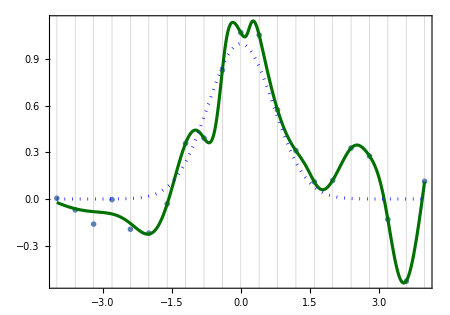
-Graphics-Figure 23. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)

RandomSeeding -> 24 (1/319, 14.1759)

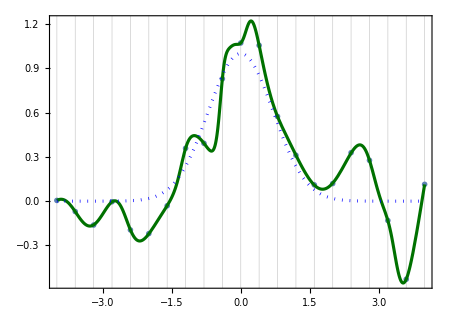
-Graphics-Figure 29. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)

### ANN fitted functions | goodness-of-fit measures

This Notebook carries out further investigations of the influence of different ANN structures on the quality of the fitting functions produced by varying the RandomSeeding setting.

$Line=$Line-1;Button["ANN fitted functions | goodness-of-fit measures", NotebookOpen[ NotebookDirectory[]<>"ANN fitted functions | goodness-of-fit measures.nb" ],Appearance->{ "Pressed"}]//Print

## Section 5: Fitting the DB Data with an InterpolatingFunction[]

```mathematica
noisyGaussianDataDB
```

```mathematica
interpFDBdata = Interpolation[noisyGaussianDataDB, InterpolationOrder->3, Method->"Hermite"]
```

codeInTextCell999[ {{"Figure",figNo},{"shows the interpolating function-based fitted model with the data in",Text[Style["noisyGaussianDataDB.",FontSize→14]]}} ]

$Line = $Line-1;
Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {interpFDBdata[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)
and InterpolationFunction (order->3).
Maximum error zero, integrated curvature `2`.",figNo++, NumberForm[ 7.97094, {6,5} ]], captionStyle] ]//Print;

differences = Table[ interpFDBdata[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ totalCurvaturePotentialEnergy[ interpFDBdata, {-4,+4} ] ]

inputGivesOutput[ integratedCurvature[ interpFDBdata, {-4,+4} ] ]

inputGivesOutput[ myArcLength[ interpFDBdata, {-4,+4} ] ]

### curvatureFunction[]

As can be seen from their respective definitions, the functions totalCurvaturePotentialEnergy[] and  curvatureFunction[] are closely related. In the following we calculate and plot the curvature of three differently specified functions.

#### Construct an InterpolatingFunction[]

Here we obtain an InterpolatingFunction[] representation of a function fitted directly to DB’s data. This function provides a “reference” value of the integrated curvature of a smooth function which does pass through all the data points, as shown below.

```mathematica
interpFDBdata = Interpolation[noisyGaussianDataDB, InterpolationOrder->4,Method->"Hermite" ]
```

$Line = $Line-1;
codeInTextCell999[ {{"Figure",figNo},{"shows the polynomial fitted model of order 12 with the data in",Text[Style["noisyGaussianDataDB.",FontSize→14]]}} ]

$Line = $Line-1;
Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {interpFDBdata[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)
and InterpolationFunction (Order->3)",figNo++], captionStyle] ]//Print;

$Line=$Line-2;differences = Table[ interpFDBdata[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ interpFDBdata, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ interpFDBdata, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ interpFDBdata, {-4,+4} ] ]

Note that the differences expressed as Egyptian fractions show that the fitted function interpFDBdata[] does pass through all the given data points.
The integrated curvature is considerably smaller than for any of the ANN fitted functions derived above.

#### Example with Head InterpolatingFunction

This constructs a Symbol kurv such that kurv[x] is the curvature function for the fitted function interpFDBdata[].

```mathematica
kurv =curvatureFunction[ interpFDBdata]/.{s$->x};
kurv[x]
```

Scaling the fitted function interpFDBdata[] makes the comparison of the two functions easier.

$Line = $Line-1;
Show[
 {
ListPlot[ Map[ (s↦{s⟦1⟧, 5 s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[{5 interpFDBdata[x], kurv[x]//Evaluate}, {x, -4,4},
PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{RGBColor[0.880722, 0.611041, 0.142051]}},
PlotRange->All,ImageSize->450,AspectRatio->0.70,PlotLegends->Placed["Expressions",Right],Frame->True, PlotPoints->200,PlotLegends->"Expressions" ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with its fitted function (InterpolationFunction of order 3)
and the corresponding curvature function.",figNo++], captionStyle] ]//Print;

This illustrates the discontinuities at two of the data points.

$Line = $Line-1;
inputGivesOutput[ {kurv[0-0.001],kurv[0],kurv[0+0.001]} ]

$Line = $Line-1;
inputGivesOutput[ {kurv[0.8-0.001],kurv[0.8],kurv[0.80+.001]} ]

codeInTextCell999[{{"Figure",figNo},{"shows that the peak curvature (~7) does not occur exactly at the data point with x = 3.6, as it might appear from Figure",figNo-1},{"above:"}} ]

$Line = $Line-1;
Show[
 {
ListPlot[ Map[ (s↦{s⟦1⟧, 5 s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[{5 interpFDBdata[x], kurv[x]//Evaluate}, {x, -4,4},
PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{RGBColor[0.880722, 0.611041, 0.142051]}},
PlotRange->All,ImageSize->450,AspectRatio->0.70,PlotLegends->Placed["Expressions",Right],Frame->True, PlotPoints->200,PlotLegends->"Expressions" ]
},
PlotRange→{{3.4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with its fitted function (InterpolationFunction of order 3)
and the corresponding curvature function, near x = 3.6.",figNo++], captionStyle] ]//Print;

inputGivesOutput[ {kurv[3.6-0.001],kurv[3.6],kurv[3.6+.001]} ]

inputGivesOutput[ kurv[3.65906] ]

There are apparent discontinuities in the curvature function at almost all the date points. The Hermite polynomial fitted function is continuous in its first derivative at each node, but not necessarily in its second derivative.

#### Examples with Head Symbol

For a simple function of the form y=f[x] where f is the Head of a defined Mathematica function and no parameters are needed, the function name only is the required argument of curvatureFunction[].

```mathematica
κ =curvatureFunction[ Sin]/.{s$->x};
κ[x]
```

$Line = $Line-1;
codeInTextCell999[ {{"Figure",figNo},{"displays",Text[Style["Sin[x]",FontSize→14]]},{"and its corresponding",Text[Style["κ[x]",FontSize→14]]},{"together (both unscaled)."}} ]

Plot[ {Sin[x], κ[x]//Evaluate}, {x, -2 π, +2 π}, PlotRange -> All, ImageSize -> 450, PlotLegends -> "Expressions", Frame -> True ]

$Line = $Line-3;
Plot[ {Sin[x],κ[x]//Evaluate}, {x, -2π,+2π},PlotRange->All, ImageSize->450, PlotLegends->"Expressions", Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. Sin[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print;

Note that …

inputGivesOutput[  κ[0]]

inputGivesOutput[  κ[π/2]]

inputGivesOutput[  κ[ -π/2]]

```mathematica
κ =curvatureFunction[ Gamma]/.{s$->x};
κ[x]
```

$Line = $Line-1;
codeInTextCell999[ {{"Figure",figNo},{"displays",Text[Style["Gamma[x]",FontSize→14]]},{"and its corresponding",Text[Style["κ[x]",FontSize→14]]},{"together, with",Text[Style["Gamma[x]",FontSize→14]]},{"scaled for ease of comparison."}} ]

Plot[ {5 Gamma[x], κ[x]//Evaluate}, {x, -3, +3}, … ]

$Line = $Line-1;
Plot[ {5 Gamma[x],κ[x]//Evaluate}, {x, -3,+3},(*PlotRange->All,*) ImageSize->450, PlotLegends->"Expressions", Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. Gamma[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print;

twoAxisPlot[{Gamma[x], κ[x]}, {x, -3, 3}, …]

$Line = $Line-3;
twoAxisPlot[{Gamma[x],κ[x]},{x,-3,3},
(*PlotRange->All,*)
ImageSize->475];
Labeled[ %, Style[ StringForm["Figure `1`. Gamma[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print

If a more elaborate specification of the target function is required—e.g., Sin[3x] instead of Sin[x]—the following is an example of how to proceed.
(Sin[3x] has been scaled for easy comparison with its curvature function κ[x].)

```mathematica
Remove[ func ]
func[x_]:=Sin[3 x]
κ =curvatureFunction[ func]/.{s$->x};
κ[x]
```

$Line = $Line-1;
codeInTextCell999[ {{"In Figure",figNo},{Text[Style["Sin[3x]",FontSize→14]]},{"and its",Text[Style["κ[x]",FontSize→14]]},{"are shown together. Curvature values for",Text[Style["Sin[3x]",FontSize→14]]},{"are 9 times (two differentiations!) larger than for",Text[Style["Sin[x].",FontSize→14]]}} ]

Plot[ {10 func[x] // Evaluate, κ[x]//Evaluate}, {x, -2 π, +2 π}, … ]

$Line = $Line-1;Plot[ {10 func[x]//Evaluate,κ[x]//Evaluate}, {x, -2π,+2π},PlotRange->All, ImageSize->450, PlotLegends->"Expressions", Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. Sin[3x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print;

twoAxisPlot[{func[x], κ[x]}, {x, -2π,+2π}, …]

$Line = $Line-3;
twoAxisPlot[{func[x],κ[x]},{x, -2π,+2π},
PlotRange->Full,
ImageSize->475];
Labeled[ %, Style[ StringForm["Figure `1`. Sin[3x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print

Note that …

$Line = $Line-2;
inputGivesOutput[  κ[0]]

$Line = $Line-2;
inputGivesOutput[  κ[π/2]]

$Line = $Line-2;
inputGivesOutput[  κ[ -π/2]]

A slightly more elaborate target function.

```mathematica
Remove[ func ]
func[x_]:=ⅇ^(-x/5)Sin[x]
κ =curvatureFunction[ func]/.{s$->x};
κ[x]
```

$Line = $Line-1;
codeInTextCell999[ {{"Figure",figNo},{"contrasts an exponentaially damped sine function and its"},{ Text[Style["κ[x].",FontSize→14]]}} ]

Plot[ {func[x] // Evaluate, κ[x]//Evaluate}, {x, -2 π, +2 π}, PlotRange -> All, ImageSize -> 450, PlotLegends -> "Expressions", Frame -> True ]

$Line = $Line-2;Plot[ {func[x]//Evaluate,κ[x]//Evaluate}, {x, -2π,+2π},PlotRange->All, ImageSize->450, PlotLegends->"Expressions", Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. ⅇ^(-x/5)Sin[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print;

twoAxisPlot[{func[x], κ[x]}, {x, -2 π, 2 π}, ImageSize -> 475]

$Line = $Line-3;
twoAxisPlot[{func[x],κ[x]},{x,-2π,2π}(*, PlotLegends->Placed[ {"func[x]","κ[x]"},Right]*),
(*PlotRange->Full,*)
ImageSize->475];
Labeled[ %, Style[ StringForm["Figure `1`. ⅇ^(-x/5)Sin[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print

Note that …

$Line = $Line-2;
inputGivesOutput[  κ[0]]

$Line = $Line-2;
inputGivesOutput[  κ[π/2]]

$Line = $Line-2;
inputGivesOutput[  κ[-π/2]]

#### Example with Head NetChain

```mathematica
Remove[ κ ]
κ[x_]:= curvatureFunction[ curvetrained159,x ]
```

Plot[ {10 curvetrained159[x], κ[x]}, {x, -4, +4}, PlotRange -> All, ImageSize -> 450, AspectRatio -> 0.70, PlotLegends -> Placed["Expressions", Right ], Frame -> True ]

$Line = $Line-1;Plot[ {10 curvetrained159[x],κ[x]}, {x, -4,+4},PlotRange->All, ImageSize->450,AspectRatio->0.70, PlotLegends->Placed["Expressions", Right ], Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained[x] with its corresponding curvature function κ[x]
		(via Plot[]; common scales).",figNo++], captionStyle] ]//Print;

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows the", Text[Style["twoAxisPlot[]",FontSize→14]]},{" version of Figure",figNo-1},{"with the full scales for both functions shown (with an x-axis for the blue function)." }}]

twoAxisPlot[ {curvetrained159[x] // HoldForm, κ[x] // HoldForm}, {x, -4, 4}, PlotRange -> All,
 ImageSize -> 475]

$Line = $Line-3;
twoAxisPlot[ {curvetrained159[x]//HoldForm,κ[x]//HoldForm},{x,-4,4},PlotRange->All,
ImageSize->475];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained[x] with its corresponding curvature function κ[x]
	        (via twoAxisPlot[]; separate scales).",figNo++], captionStyle] ]//Print

Note that …

$Line = $Line-2;
inputGivesOutput[  κ[0]]

$Line = $Line-2;
inputGivesOutput[  κ[-0.2]]

$Line = $Line-2;
inputGivesOutput[  κ[ +0.2]]

$Line = $Line-2;
inputGivesOutput[  κ[ -4]]

$Line = $Line-2;
inputGivesOutput[  κ[ +4]]

## Section 6: Fitting & Evaluating Polynomial Models

Experimentation showed that the best compromise in determining the order of a polynomial fitted function that:
(i) gave large maximum errors (order too low), and
(ii) exhibited large and unnecessary excursions between data points (order too high)
was of 12^th order.

```mathematica
polyOrder=13;
nlm=NonlinearModelFit[noisyGaussianDataDB,Array[ coeff, polyOrder].Table[ x^n, {n, 0,polyOrder-1} ],Array[ coeff, 21],x];
Normal[nlm]
```

```mathematica
Remove[ polyModel ]
polyModel[x_] := Normal[nlm]//Evaluate
polyModel[x]
```

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows the polynomial fitted model of order 12 with the data in"},{Text[Style["noisyGaussianDataDB.",FontSize→14]]}} ]

$Line = $Line-1;
Show[
 {
ListPlot[ Map[ (s↦{s⟦1⟧, s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[polyModel[x],{x,-4,4},PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70,
PlotLegends->Placed["Expressions",Right]]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with a best-fit 12^th order polynomial.",figNo++], captionStyle] ]

The function kurvPoly[] is a pure function representation of the curvature function of the polynomial model polyModel[].

```mathematica
kurvPoly = curvatureFunction[ polyModel ]/.{s$->x};
kurvPoly[x]
```

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows the (scaled) polynomial fitted model of order 12 and its (unscaled) curvature function with the data in"},{Text[Style["noisyGaussianDataDB.",FontSize→14]]}} ]

$Line = $Line-3;
Show[
 {
ListPlot[ Map[ (s↦{s⟦1⟧, 10 s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[{10 polyModel[x],kurvPoly[x]},{x,-4,4},PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70,
PlotLegends->Placed["Expressions",Right]]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with a (scaled) best-fit 12^th order polynomial
and its corresponding curvature function.",figNo++], captionStyle] ]//Print

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"—as shown below in the next Program cell—is produced by the IP package function", Text[Style["twoAxisPlot[],",FontSize→14]]},{"which allows two functions to be plotted together with separate scales."}} ]

Show[
 {
twoAxisPlot[{polyModel[x],kurvPoly[x]},{x,-4,4}, PlotLegends->Placed[ {"polyModel[x]","kurvPoly[x]"},Right],
PlotRange->All,
ImageSize->475,
AspectRatio->0.7],
ListPlot[ Map[ (s↦{s⟦1⟧, s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}]
},
GridLines→{Table[  k, {k, -4,+4, 0.4}],None}]

$Line = $Line-3;
Show[
 {
twoAxisPlot[{polyModel[x]//HoldForm,kurvPoly[x]//HoldForm},{x,-4,4}, (*PlotLegends->Placed[ {"polyModel[x]","kurvPoly[x]"},Right],*)
PlotRange->All,
ImageSize->475,
AspectRatio->0.7],
ListPlot[ Map[ (s↦{s⟦1⟧, s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}]
},
GridLines→{Table[  k, {k, -4,+4, 0.4}],None}];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with a (scaled) best-fit 12^th order polynomial
and its corresponding curvature function.",figNo++], captionStyle] ]//Print

$Line=$Line-2;differences = Table[ polyModel[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ polyModel, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ polyModel, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ polyModel, {-4,+4} ] ]

Here are the corresponding goodness-of-fit measures for curvetrained159:

$Line=$Line-2;differences = Table[ curvetrained159[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line=$Line-2;
inputGivesOutput[ totalCurvaturePotentialEnergy[ curvetrained159, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained159, {-4,+4} ] ]

$Line=$Line-2;
inputGivesOutput[ myArcLength[ curvetrained159, {-4,+4} ] ]

For all measures except the minimum and maximum errors, the polynomial model is superior to the ANN-derived model.

$Line = $Line-3;
Show[
 {
twoAxisPlot[{curvetrained159[x]//HoldForm,polyModel[x]//HoldForm},{x,-4,4}, (*PlotLegends->Placed[ {"polyModel[x]","kurvPoly[x]"},Right],*)
PlotRange->All,
ImageSize->475,
AspectRatio->0.7],
ListPlot[ Map[ (s↦{s⟦1⟧, s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}]
},
GridLines→{Table[  k, {k, -4,+4, 0.4}],None}];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained159[x] and polyModel[x]
	(via twoAxisPlot[]; separate scales).",figNo++], captionStyle] ]//Print

$Line = $Line-3;
Show[
 {
Plot[{curvetrained159[x]//HoldForm,polyModel[x]//HoldForm},{x,-4,4}, (*PlotLegends->Placed[ {"polyModel[x]","kurvPoly[x]"},Right],*)
PlotRange->All,
ImageSize->475,
AspectRatio->0.7,
Frame->True,
PlotLegends→Placed[{"curvetrained159[x]","polyModel[x]"},Right]
],
ListPlot[ Map[ (s↦{s⟦1⟧, s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}]
},
GridLines→{Table[  k, {k, -4,+4, 0.4}],None}];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained159[x] and polyModel[x]
	(via Plot[]; common scales).",figNo++], captionStyle] ]//Print